# Exploring Food Data

Corwin Kerr

The Wolfram Language has a built-in knowledge base to feed WolframAlpha. I was curious about exploring the data associated with food and ended up exploring smoothie drink colors.

## What data is available?

Free form input can be used to start the search for available data:

```mathematica
strawberry=LinguisticAssistant
```

And see what this is behind the scenes:

```mathematica
%//InputForm
```

Entity["Food", {EntityProperty["Food", "FoodType"] -> 
   ContainsExactly[{Entity["FoodType", "Strawberry"]}], 
  EntityProperty["Food", "AddedFoodTypes"] -> 
   ContainsExactly[{}]}]

There is a difference between Food, FoodType, and FoodTypeGroup. “Food” has the most properties that we can query.

```mathematica
{foodProperties,foodTypeProperties,foodTypeGroupProperties}=EntityProperties[#]&/@{"Food","FoodType","FoodTypeGroup"};
Length/@%
```

{627,32,12}

### The Role of FoodTypeGroup

We can see the 31 FoodTypeGroup which are available.

```mathematica
foodTypeGroup=EntityValue["FoodTypeGroup","Entities"]
```

{alcoholic beverages,berries,breads,candies,carbonated beverages,cheeses,coffee beverages,drinks,fats,fishes,frozen novelties,fruits,greens,juices,meats,milks,nuts,oils,pastas,plants,poultry,preserves,roes,sandwiches,sauces,seafood,seeds,soups,soy,spices,squashes}

Some contain more elements than others...

```mathematica
Length/@EntityValue[foodTypeGroup,"Foods"]
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

{646,86,1232,1825,415,633,1,2802,347,1093,613,6131,209,1190,1,1872,1185,1319,1377,2676,2553,149,39,283,1009,1,5137,1050,72,3,288}

## Making a Smoothie

Say we are interested in making a smoothie, and we need to understand the densities of fruits we pick.

```mathematica
foodTypesOfInterest={Entity["FoodTypeGroup","Fruits"],Entity["FoodTypeGroup","Greens"],Entity["FoodTypeGroup","Juices"]};
```

We can define a function to get densities of food types, being careful to ignore the foods with missing values.

```mathematica
densityOfFoodType[type_]:=EntityValue[EntityValue[type["Foods"]],"Density","NonMissingEntityAssociation"]
SetAttributes[densityOfFoodType,Listable]
```

```mathematica
densityOfFoodType[Entity["FoodTypeGroup","Greens"]]
```

<|Beet greens, cooked, boiled, drained, without salt→0.608652 g/cm^3,Beet greens, cooked, boiled, drained, with salt→0.608652 g/cm^3,Beet greens, raw→0.160617 g/cm^3,Chicory greens, raw→0.122576 g/cm^3,Collards, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, without salt→0.760816 g/cm^3,Collards, frozen, chopped, cooked, boiled, drained, with salt→0.760816 g/cm^3,Collards, frozen, chopped, unprepared→0.760816 g/cm^3,Collards, raw→0.152163 g/cm^3,Dandelion greens, cooked, boiled, drained, without salt→0.443809 g/cm^3,Dandelion greens, cooked, boiled, drained, with salt→0.443809 g/cm^3,Dandelion greens, raw→0.232471 g/cm^3,Mustard greens, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, cooked, boiled, drained, without salt→0.614288 g/cm^3,Mustard greens, frozen, unprepared→0.614288 g/cm^3,Mustard greens, raw→0.236698 g/cm^3,Pumpkin leaves, cooked, boiled, drained, without salt→0.300099 g/cm^3,Pumpkin leaves, cooked, boiled, drained, with salt→0.300099 g/cm^3,Pumpkin leaves, raw→0.164843 g/cm^3,Spices, bay leaf→0.12173 g/cm^3,Turnip greens, canned, no salt added→0.98906 g/cm^3,Turnip greens, canned, solids and liquids→0.98906 g/cm^3,Turnip greens, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, cooked, boiled, drained, without salt→0.98906 g/cm^3,Turnip greens, frozen, unprepared→0.98906 g/cm^3,Turnip greens, raw→0.232471 g/cm^3|>

We generate a list of associations with one element each for our foods of interest.

```mathematica
den=densityOfFoodType[foodTypesOfInterest];
```

We can visualize the density of fruits.

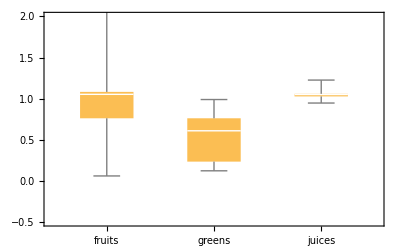

```mathematica
BoxWhiskerChart[den,PlotRange->{-.5,2},ChartLabels->{"fruits","greens","juices"}]
```

It looks like greens tend to be much less dense, but what is the fruit with the ridiculous density?  Here are the outlying fruit items, which have a density greater than that of lead (11.34 "g""/"("cm")^3)! This must be an error.

```mathematica
Select[den[[1]],#>Entity["Element","Lead"][EntityProperty["Element","Density"]]&]
```

<|PREGO Pasta, Chunky Garden Tomato, Onion and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3,PREGO Pasta, Tomato, Basil and Garlic Italian Sauce, ready-to-serve→17.5833 g/cm^3|>

## Fruit Color Space

I decided to investigate the colors of smoothies one could make from different kinds of ingredients.

```mathematica
insideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalInsideColors"]
SetAttributes[insideColorsetOfFoodType,Listable]
```

```mathematica
outsideColorsetOfFoodType[type_]:=EntityValue[type,"TypicalOutsideColors"]
SetAttributes[outsideColorsetOfFoodType,Listable]
```

```mathematica
rgbFromColorset[set_]:=EntityValue[set,EntityProperty["ColorSet","TypicalColorValue"]]
```

Apples have certain exterior colors given as names:

```mathematica
outsideColorsetOfFoodType[]
```

{brown,cream,green,red,white,yellow}

We get representative instances of these colors.

```mathematica
rgbFromColorset@%
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Note that we can also see their interior colors, which aren’t quite as pretty.

```mathematica
rgbFromColorset@insideColorsetOfFoodType[]
```

{RGBColor[0.6, 0.4, 0.2],RGBColor[1., 0.992157, 0.815686],RGBColor[1, 1, 1],RGBColor[1, 1, 0]}

Generate a 3D span of the exterior in XYZ color space and display it in 2D color space:

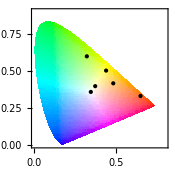

```mathematica
ChromaticityPlot[rgbFromColorset[outsideColorsetOfFoodType[]],PlotStyle->Black]
```

Define functions to generate instances of possible fruit colors based on its exterior colors .

```mathematica
fruitColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[outsideColorsetOfFoodType[fruit]],"XYZ"]
fruitInsideColorList[fruit_]:=List@@@ColorConvert[rgbFromColorset[insideColorsetOfFoodType[fruit]],"XYZ"]
fruitColorHull[fruit_]:=ConvexHullMesh[fruitColorList[fruit]]
```

Here we generate a lot of possible apple colors by picking random points within the color space.

```mathematica
applecolors=XYZColor@@@RandomPoint[fruitColorHull[],100]
```

{XYZColor[0.5380962494246048, 0.5651557122070013, 0.08317889883357721],XYZColor[0.5598139588019678, 0.7715310812504527, 0.24173993481921874],XYZColor[0.8772219594171907, 0.9275251200025681, 0.5320950498318225],XYZColor[0.46339668801631884, 0.39200474050642564, 0.17063145765698184],XYZColor[0.7392081911911407, 0.8126873217567482, 0.48041952625337825],XYZColor[0.4652607069442364, 0.5439857906648421, 0.12115543576166643],XYZColor[0.6847232085815699, 0.6683764235117721, 0.13583252212816987],XYZColor[0.7253830404593701, 0.8589903676610074, 0.10401953975519096],XYZColor[0.5669255637012186, 0.7328188703212012, 0.21770276243900077],XYZColor[0.4232051331790152, 0.3401792588504361, 0.16458048561527072],XYZColor[0.4397701125781187, 0.3214470291034838, 0.07802356759494011],XYZColor[0.5868909956650706, 0.613034236962733, 0.30080250007951725],XYZColor[0.6151975987408861, 0.7251429254609857, 0.20629292075350658],XYZColor[0.47640280395006906, 0.3807903152018314, 0.08411558234271665],XYZColor[0.7877335829081576, 0.8352292958609308, 0.5946292073226814],XYZColor[0.5119983372758282, 0.3590251267307437, 0.06098293596256554],XYZColor[0.4864303874406749, 0.34535944408806685, 0.10538870265223743],XYZColor[0.4614464757787272, 0.5469510885567735, 0.11840624801158961],XYZColor[0.529055380966046, 0.640181354623374, 0.23118634484957779],XYZColor[0.903159420983065, 0.9259284758475218, 0.7347107165467249],XYZColor[0.34788127636947475, 0.4894358905533699, 0.09652516787888354],XYZColor[0.6500618827371368, 0.7536786144317454, 0.41308360003630173],XYZColor[0.5793914228924729, 0.6298709974405511, 0.08583034954557678],XYZColor[0.4566155501457304, 0.581283632251549, 0.21480725161670866],XYZColor[0.6664988368785604, 0.7056916953810729, 0.13047579516772911],XYZColor[0.5871526290611432, 0.5952670289861711, 0.4157200361939045],XYZColor[0.5999112907094634, 0.5707113005765506, 0.2922714903559521],XYZColor[0.3358188981777952, 0.29627291798962674, 0.09678425314339312],XYZColor[0.43972047974389017, 0.5808711131798064, 0.09958768895595682],XYZColor[0.5762728195803345, 0.6955077093166074, 0.152444311790638],XYZColor[0.3943658454994947, 0.4553870609663323, 0.21027698850795773],XYZColor[0.8971881786514259, 0.9412174196310964, 0.6591846992974163],XYZColor[0.7292935877773584, 0.6809157373489761, 0.49941935869611787],XYZColor[0.4980086107114766, 0.7385330212367899, 0.21548677122601878],XYZColor[0.43861606438159584, 0.432977490563374, 0.0704426095933286],XYZColor[0.5087755477637191, 0.7081654326527801, 0.09896921924837654],XYZColor[0.8990734653078983, 0.9249583964010258, 0.711016905615311],XYZColor[0.48782676481434784, 0.5799014813344575, 0.07889185981863955],XYZColor[0.6038799262634257, 0.6685881524161125, 0.3982895809395689],XYZColor[0.5586152970894073, 0.747800034463021, 0.32679334998878284],XYZColor[0.5306520693484337, 0.5664939339217322, 0.08648310784631341],XYZColor[0.5181648448503381, 0.6756920965012622, 0.09484144443501963],XYZColor[0.4908289325091494, 0.5437029580216804, 0.27225634122580555],XYZColor[0.7231398418968641, 0.7719181032246992, 0.43920323167491115],XYZColor[0.5312217917790211, 0.40698424990215, 0.20219085004382642],XYZColor[0.7709877894376368, 0.8441200675609531, 0.431082159730792],XYZColor[0.5818970503496282, 0.4919739949255756, 0.08242162021937949],XYZColor[0.45998057826909144, 0.37779842715701883, 0.09622992417724463],XYZColor[0.26723293343890964, 0.22846824196639282, 0.04780116682488522],XYZColor[0.6857229805610087, 0.7686649900445451, 0.4204408454605165],XYZColor[0.6318394528788148, 0.6769577600110589, 0.2599545072626409],XYZColor[0.677493050472113, 0.6992211562212783, 0.4276043779299924],XYZColor[0.5200089713982942, 0.5226088610098544, 0.22183606992319593],XYZColor[0.4578855892401593, 0.5543306039094767, 0.19390611909784372],XYZColor[0.5446752499581365, 0.45048134501557857, 0.14229297386413586],XYZColor[0.6314332509279884, 0.6060371467924434, 0.265816513587514],XYZColor[0.4818885381789041, 0.5450543263891904, 0.2917523877482596],XYZColor[0.4599902461557589, 0.3371344247220528, 0.0784481133412751],XYZColor[0.6784167079807494, 0.7684456901732098, 0.17154638104805187],XYZColor[0.7037236325086879, 0.7955564908285092, 0.113227351830125],XYZColor[0.46476751149573314, 0.747646783594465, 0.10623632920192805],XYZColor[0.5439297159326802, 0.5037471388304212, 0.24900974859363567],XYZColor[0.50315960957479, 0.7271463083613653, 0.1634196187269561],XYZColor[0.6222109941067894, 0.765106907288784, 0.20989510425363667],XYZColor[0.3657950896756258, 0.33141928474118554, 0.09052787770341197],XYZColor[0.767711077683329, 0.8557869341041927, 0.47085123800942486],XYZColor[0.6920010110308249, 0.8298908276182034, 0.3905807872004977],XYZColor[0.6521895712679618, 0.6562060146683363, 0.12713060739348714],XYZColor[0.8538645536052144, 0.8918419293503074, 0.5052544576382704],XYZColor[0.7267424763638012, 0.7037875306272906, 0.3947043268792302],XYZColor[0.39696117560063526, 0.25492387957422746, 0.06303748803626552],XYZColor[0.4561204643430711, 0.4680294114735474, 0.05538466119583918],XYZColor[0.4914852804350959, 0.45727303478138814, 0.06873057177265762],XYZColor[0.5735489016543273, 0.7691458887810155, 0.3148437022433278],XYZColor[0.6717437418680002, 0.7725554913200338, 0.22703229377199363],XYZColor[0.6231048079213642, 0.8219201414407394, 0.24427758080739037],XYZColor[0.5171326149475634, 0.7565962644827017, 0.1024299108031066],XYZColor[0.6072182449298024, 0.7044906185199448, 0.10418405790196827],XYZColor[0.4095762014277161, 0.47908665664190087, 0.12251865453300959],XYZColor[0.44433882744188324, 0.5586060750804537, 0.11717492627860004],XYZColor[0.6594746294269015, 0.8396542837253017, 0.2832640373429688],XYZColor[0.7414542258641735, 0.8169705306491125, 0.23979753054957087],XYZColor[0.675003393739601, 0.7126790417661718, 0.11422569374378888],XYZColor[0.5571677116359196, 0.5392522569527313, 0.22164825044519232],XYZColor[0.4904782515294256, 0.6795255449189413, 0.16485960326285376],XYZColor[0.6467450438628012, 0.639518939093226, 0.20321706521164284],XYZColor[0.7451133351006335, 0.8444152359314275, 0.3411549962683814],XYZColor[0.5679556434411067, 0.744391324707845, 0.2554371099495537],XYZColor[0.6421583181157932, 0.7734584045714542, 0.15431069412504805],XYZColor[0.7111350118041421, 0.8234070326673165, 0.2992347850801048],XYZColor[0.8914295086791074, 0.912426786638672, 0.677537199592723],XYZColor[0.4924674655694442, 0.3982550444543479, 0.05074876281317742],XYZColor[0.5554506591672482, 0.629248089435314, 0.1609233072073677],XYZColor[0.776118137439833, 0.7938904316878003, 0.4724719399285523],XYZColor[0.6016754259861873, 0.4892177035534998, 0.21950789953062888],XYZColor[0.8720540725326226, 0.9087626482328889, 0.5700925294572977],XYZColor[0.810126312767396, 0.8725703532425214, 0.4016900670182927],XYZColor[0.7508614187774915, 0.8556450622289254, 0.28442605690173195],XYZColor[0.611068327276841, 0.5767582575484193, 0.15200985092827635],XYZColor[0.7841505992858601, 0.8033077863473411, 0.39072586326998426]}

And visualize them in 3D and 2D space:

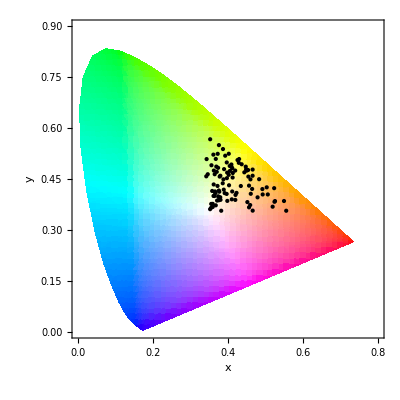
-Graphics3D-
-Graphics-

```mathematica
{ChromaticityPlot3D[#],ChromaticityPlot[#,PlotStyle->Black]}&[applecolors]//TableForm
```

To visualize the possible colors in a combination of fruits, we combine the color lists of our fruits of interest. I’m using Interpreter to get the entities for the string inputs.

```mathematica
cols=fruitColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"};
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.5725801900229782, 0.6122810589005939, 0.1617373369162477],XYZColor[0.36622859270035957, 0.23159315917368384, 0.08167650607780874],XYZColor[0.31812307495859027, 0.26422961615741125, 0.6997194425266055],XYZColor[0.3788517775488428, 0.5141482575652937, 0.08870495143608148],XYZColor[0.6920733150579473, 0.6985687898790526, 0.6339161346308527],XYZColor[0.19561900548615918, 0.11986633793889345, 0.11410686081768229],XYZColor[0.5460627869125837, 0.7813720396778397, 0.17702430331406982],XYZColor[0.6803300081280726, 0.6199374560567633, 0.5475060015927901],XYZColor[0.2664895981269265, 0.15619715719808125, 0.4710613059569332],XYZColor[0.6746298300911505, 0.7887436158577473, 0.4228342571279483],XYZColor[0.37091124414126664, 0.21846815294828736, 0.07884371055172334],XYZColor[0.44302089291941027, 0.33038001450699317, 0.21794385785321346],XYZColor[0.7113103328802876, 0.8152616582257587, 0.3483864305442518],XYZColor[0.5608138059040672, 0.5775225771794085, 0.5234661683994003],XYZColor[0.21638971271032148, 0.15943027044225533, 0.5699274503046946],XYZColor[0.685132842968914, 0.7465265035921248, 0.32192754819848524],XYZColor[0.2590273290840793, 0.19458237412485435, 0.047664022779089654],XYZColor[0.45840037224765806, 0.4102698191714259, 0.5403487204027991],XYZColor[0.7847126228218876, 0.7809661571568022, 0.5668610256017707],XYZColor[0.18961483433908033, 0.17023125084211987, 0.5057579872551744],XYZColor[0.3449709872992678, 0.3702571524160253, 0.11680947995602153],XYZColor[0.27995247084793984, 0.17829376045618084, 0.07220405220111104],XYZColor[0.11888334838274861, 0.08106436386618532, 0.08245081318645531],XYZColor[0.48754022068385205, 0.3243148665837535, 0.06289217532433589],XYZColor[0.3807648051794358, 0.27924851243893245, 0.1125920995610914],XYZColor[0.25011947788816047, 0.13650919976441023, 0.1372827254066391],XYZColor[0.4958869547121493, 0.5803374193166985, 0.3593512468473353],XYZColor[0.8126679475180262, 0.9205239943756119, 0.6103044663722289],XYZColor[0.7406564273770472, 0.7086689967715464, 0.503655577700547],XYZColor[0.19921882234052968, 0.10286676193307487, 0.44509462118719323],XYZColor[0.7321750591716233, 0.7697828710686409, 0.3911123530750412],XYZColor[0.2998183319627491, 0.39495657000181883, 0.2590136700822171],XYZColor[0.17757246686736938, 0.24833450699441528, 0.06270589743198329],XYZColor[0.6321961168008995, 0.6569096515882421, 0.47115303349343785],XYZColor[0.4296354735350486, 0.3333146998340498, 0.3986995038950619],XYZColor[0.5647230430232842, 0.6116803917714343, 0.6349516246957093],XYZColor[0.07136558056472031, 0.04917652052197863, 0.07064464727615849],XYZColor[0.440029769415898, 0.3999812284725154, 0.6157131447167054],XYZColor[0.33418584037069266, 0.3892839567362806, 0.21430077705892991],XYZColor[0.5190715931718731, 0.5682167332836597, 0.10094744689935453],XYZColor[0.45736446624924476, 0.40089001709545, 0.16807817468946507],XYZColor[0.20546194715660626, 0.23293269055384325, 0.3098760039295728],XYZColor[0.3537446994302361, 0.19471742782711543, 0.08257063719462832],XYZColor[0.13076971031525686, 0.06454150459607855, 0.26835338390900965],XYZColor[0.7527347966348176, 0.8212704694092378, 0.43636465449566575],XYZColor[0.43881941709546457, 0.5636697911150844, 0.36952519184363186],XYZColor[0.65030624129743, 0.6222610480785004, 0.10819780795838063],XYZColor[0.5045402994021294, 0.7335948685616404, 0.1022462870576698],XYZColor[0.14146765894357005, 0.11498466310224342, 0.04464300159251322],XYZColor[0.5146490572075103, 0.6815741157226666, 0.2558854237728557],XYZColor[0.585095638960179, 0.6261543013349767, 0.1369320824022926],XYZColor[0.5154590744039617, 0.5260753875353826, 0.5626323577740081],XYZColor[0.5642035681382688, 0.7790095983419941, 0.1999617336934919],XYZColor[0.38294592484543644, 0.24142802371160987, 0.20001679320303356],XYZColor[0.41966424035917005, 0.45098706414118406, 0.1924442816218933],XYZColor[0.3118366552214781, 0.4189689622549765, 0.09229420351645656],XYZColor[0.8612708738816827, 0.921134967394286, 0.7052332371558051],XYZColor[0.30630953355952906, 0.1537493315967774, 0.2539267037205283],XYZColor[0.16394218321216047, 0.11684892712895911, 0.2588772437842167],XYZColor[0.620802363481609, 0.7845619143169705, 0.19349797953096026],XYZColor[0.1378254840366161, 0.09070427396127922, 0.5124602936721622],XYZColor[0.34416889794921846, 0.47122532415406637, 0.19457280157747492],XYZColor[0.632257081489458, 0.7752874455527367, 0.19646302144348382],XYZColor[0.4421759869996794, 0.4064718265909907, 0.13308737056471598],XYZColor[0.5024732445030274, 0.5367555033771748, 0.6469618062923782],XYZColor[0.23684270720392264, 0.2149869909818255, 0.072785040489589],XYZColor[0.3701130868526957, 0.5475288974049598, 0.32792721230266986],XYZColor[0.5556042207379169, 0.7987079144208756, 0.17037939274570668],XYZColor[0.3809635379093558, 0.23713884401224472, 0.0860508489028401],XYZColor[0.1071101213241249, 0.10774350210984596, 0.08574942725852142],XYZColor[0.3688405214259357, 0.3758688862848919, 0.23545656944096283],XYZColor[0.45889709350833374, 0.5303242414532406, 0.3206405963904625],XYZColor[0.2840806342922305, 0.3326679399190481, 0.458870667542424],XYZColor[0.13000837272369392, 0.15922992738844666, 0.23913753247378688],XYZColor[0.2583003759107324, 0.39284325322834246, 0.09497302474301283],XYZColor[0.3788833751752324, 0.3371211698360367, 0.4178227301463987],XYZColor[0.3941234605034337, 0.43228253665604577, 0.23772909165720313],XYZColor[0.7992812772767176, 0.8967414946234543, 0.5295966141380571],XYZColor[0.4866054736930502, 0.4913080325764715, 0.3697044520959526],XYZColor[0.4762881039966508, 0.7506570153778186, 0.11092117965108561],XYZColor[0.23631050455491176, 0.3062191554555854, 0.2590718505531068],XYZColor[0.5349036099771701, 0.5135808657204871, 0.5565019761080116],XYZColor[0.46719801244930836, 0.449402747251758, 0.41804680213396084],XYZColor[0.3709446441904164, 0.21616144451719743, 0.08061561276444729],XYZColor[0.3988084241943134, 0.36170640465276815, 0.2856660373647256],XYZColor[0.7767280945417604, 0.8618146739833566, 0.17145228257896106],XYZColor[0.6942064255022998, 0.8209164854178564, 0.43764264166700706],XYZColor[0.6378089054660568, 0.6824819040772655, 0.6840208919488188],XYZColor[0.17003589388482, 0.1541239945108871, 0.42343386476936173],XYZColor[0.44274695998107394, 0.2753263430795546, 0.0771021056499771],XYZColor[0.41380672098702986, 0.36690109596778486, 0.14914783207982518],XYZColor[0.33744672336190906, 0.5399682760430237, 0.11218136742863527],XYZColor[0.5356959351821081, 0.6436366621635755, 0.49446395021007794],XYZColor[0.17695619879295588, 0.30416128037959356, 0.10680169152713548],XYZColor[0.16750808749305157, 0.09005168953299847, 0.07310251893311448],XYZColor[0.48594463538365884, 0.4389514038773431, 0.6007280990336604],XYZColor[0.5241242598681178, 0.7272335011374856, 0.2849534348029855],XYZColor[0.4453141677921041, 0.5352232645742782, 0.09786012413841494],XYZColor[0.6695147899183415, 0.6879926970552063, 0.13075162180085165],XYZColor[0.35086333583895646, 0.3944478919218509, 0.3965656316635232]}

Mixtures of pure fruit colors spans a good deal of the space. However, this is based on the generic color names and doesn’t take into account the likely muted actual values.

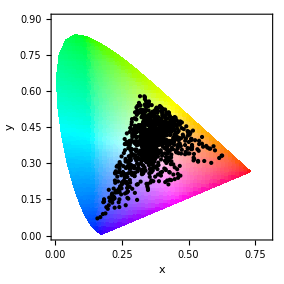

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],1000],PlotStyle->Black]
```

We can try doing the same with interior colors.

```mathematica
innerColors=fruitInsideColorList[Interpreter["Food"][#]]&/@{"Apple","Orange","Carrot","Banana","Blueberry","Blackberry","Strawberry"};
XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[cols,1]],100]
```

{XYZColor[0.6417755303598359, 0.5918190724145876, 0.5329626337479462],XYZColor[0.5542672578974518, 0.5904288478312115, 0.20082979902734477],XYZColor[0.32436780881316973, 0.33196709033919436, 0.3709201132281429],XYZColor[0.6266669467257974, 0.597762742973378, 0.14643932659899195],XYZColor[0.3028808178839074, 0.27004673975876103, 0.5137316548435426],XYZColor[0.4403882887293872, 0.5400090148445343, 0.15658464364484137],XYZColor[0.4904625749663044, 0.3960760865970917, 0.3231354269090977],XYZColor[0.48503322298380336, 0.41788201980686257, 0.17046791376355408],XYZColor[0.7131682327117684, 0.7529716333422475, 0.3804468142379308],XYZColor[0.6827355231218678, 0.8504906462958534, 0.38976609023879616],XYZColor[0.12072375947928216, 0.1843440300090008, 0.1355855382467024],XYZColor[0.7108788763815489, 0.8351912313970756, 0.2758944519730314],XYZColor[0.571529556992857, 0.5380910010574317, 0.39900011755788045],XYZColor[0.6482383728611399, 0.6139711029351039, 0.5966801605685433],XYZColor[0.30657654259970457, 0.41904806449593746, 0.24874030013884296],XYZColor[0.20700455938310613, 0.20493717451366378, 0.40660681020941614],XYZColor[0.6568087420358647, 0.7852114887482052, 0.15319714993944045],XYZColor[0.8100086105618532, 0.8918761067333386, 0.6329970822680914],XYZColor[0.37686820602948135, 0.32905035642299085, 0.37128570346112],XYZColor[0.4989314263475294, 0.5204753659770501, 0.3738091342529747],XYZColor[0.4495526582842627, 0.40221193783910103, 0.6693974714068817],XYZColor[0.6703352764795928, 0.810928892388325, 0.21195809087083994],XYZColor[0.506602107493774, 0.5904503082703635, 0.38971922915163015],XYZColor[0.3474527664482855, 0.3422654480219577, 0.27996169403386995],XYZColor[0.5998271174136619, 0.5381116676886929, 0.20458689327523405],XYZColor[0.4098241827408703, 0.3836179924205919, 0.1465317971049349],XYZColor[0.5640226154739428, 0.6156063523182626, 0.25987341304332745],XYZColor[0.768686980526946, 0.7761443918499816, 0.5008809735428205],XYZColor[0.19480369262145236, 0.2078662410005604, 0.1010162761015353],XYZColor[0.7232360988841767, 0.7991540403919769, 0.31539356859147294],XYZColor[0.2649748187267197, 0.17660220834188933, 0.04436666895909369],XYZColor[0.509597548278189, 0.6596135058744798, 0.18093415388776346],XYZColor[0.15713486795557519, 0.1106050550922234, 0.49129639990720475],XYZColor[0.4711185193305628, 0.49951178999476176, 0.2579678032875715],XYZColor[0.1802514735502735, 0.2684530003544435, 0.20967768673333798],XYZColor[0.2717017282317623, 0.18581368535636755, 0.26394701479049554],XYZColor[0.7154635727831985, 0.7853157834960068, 0.5219553039477484],XYZColor[0.5624245000037217, 0.5371706769315289, 0.4881229990870356],XYZColor[0.19500741786418307, 0.1360564181611411, 0.5257166300512542],XYZColor[0.18461289680997883, 0.2906520048987028, 0.051083782454837134],XYZColor[0.6551019645717006, 0.6505759872232132, 0.2960081340947115],XYZColor[0.3771631885305272, 0.30776836956056475, 0.5881943375828168],XYZColor[0.6263550468531477, 0.5421430000821365, 0.39990345936237814],XYZColor[0.7242763911294788, 0.8197550363083325, 0.10271628870131222],XYZColor[0.6886279747578342, 0.680117298678455, 0.2585566706439292],XYZColor[0.2620515398296902, 0.1889021291336811, 0.2928854487676372],XYZColor[0.5563340476895066, 0.6979898520230495, 0.4269815219000298],XYZColor[0.37340833875052926, 0.4033038708374824, 0.602522546279978],XYZColor[0.36373990640700027, 0.6629737329317312, 0.10162075197019094],XYZColor[0.5067507923978941, 0.5433318069356811, 0.17350411866839444],XYZColor[0.5580289215362039, 0.6788041375035786, 0.4247610187485352],XYZColor[0.24640053122094308, 0.1882277175161754, 0.10351251627054969],XYZColor[0.5303555008975941, 0.5170842391350913, 0.46371027458356295],XYZColor[0.3680938626513107, 0.5116689195158562, 0.3906645120988387],XYZColor[0.6269670754265398, 0.7769039506272376, 0.4993905441286083],XYZColor[0.2052876790861703, 0.13159406654321637, 0.7177843589512886],XYZColor[0.1968784252255683, 0.27639297314442424, 0.12934185632916928],XYZColor[0.9039407696152929, 0.9659530040941874, 0.65533229117142],XYZColor[0.4072139068572743, 0.21529753687056818, 0.07562537539265524],XYZColor[0.33335210676517, 0.3375328555313407, 0.0753612937800957],XYZColor[0.3182884413026882, 0.2539395110486863, 0.697877708355756],XYZColor[0.3611033471375581, 0.2969062203873437, 0.5340986375457045],XYZColor[0.3643812951548183, 0.3083184959225017, 0.42635530741200445],XYZColor[0.41677016016429336, 0.4271436617916965, 0.4212205446951248],XYZColor[0.37255697539399224, 0.37854180953082295, 0.07718502056262022],XYZColor[0.7529379207766672, 0.7687149554104596, 0.7776631562261155],XYZColor[0.8168250100697684, 0.9058463932057227, 0.2649147949376326],XYZColor[0.47861902717988125, 0.526821644924062, 0.36980767792295344],XYZColor[0.45890491688525337, 0.3741371981004754, 0.23612923969414668],XYZColor[0.7152897684585405, 0.8724114082856308, 0.10815535751593142],XYZColor[0.5160182827534027, 0.5167392290248786, 0.4099853800964445],XYZColor[0.37962095722247635, 0.5624985301147801, 0.07872869078536593],XYZColor[0.4264350469265691, 0.3429917886333357, 0.14311363097509577],XYZColor[0.16732309348994445, 0.09724668855695662, 0.01252560716872897],XYZColor[0.19972970839886017, 0.32317665107232585, 0.19276173326014356],XYZColor[0.5823028151747071, 0.6300911237372754, 0.13626589080483886],XYZColor[0.43791229010284216, 0.43423555657364143, 0.24926857568817018],XYZColor[0.20880255307767592, 0.15440403984832718, 0.5161108646096765],XYZColor[0.5963012221748499, 0.764522533953223, 0.3796537454098575],XYZColor[0.4790929017462989, 0.5175769847344992, 0.6061057348690656],XYZColor[0.43912880799266574, 0.35012871117678157, 0.1168737122751532],XYZColor[0.14872240856300445, 0.25778936494203963, 0.09400535686418243],XYZColor[0.318956617529531, 0.23658646918243964, 0.029871095064710862],XYZColor[0.35544129574378525, 0.3631213929415994, 0.08535559876235221],XYZColor[0.2055966310096592, 0.23137446089587554, 0.3626546319172915],XYZColor[0.3399283052918708, 0.37290586735577824, 0.4366653584498775],XYZColor[0.4302267833773322, 0.40149648667593196, 0.5936941008836142],XYZColor[0.4916887857250877, 0.5716179578255917, 0.3637904810829854],XYZColor[0.6429855318877261, 0.6670117439779676, 0.21498937463303414],XYZColor[0.6030398494966672, 0.581332658729336, 0.32159057129461976],XYZColor[0.19668838553505685, 0.13750840397550357, 0.6358202441405915],XYZColor[0.23340479745207932, 0.127056340943552, 0.2504259445607898],XYZColor[0.371717929987906, 0.4254576729821423, 0.17814293453965047],XYZColor[0.8800514772551805, 0.9053510340323313, 0.6112447735487035],XYZColor[0.28313598182488764, 0.24974179864514368, 0.02956906013031302],XYZColor[0.7091292654793776, 0.8446526679850793, 0.11592575009354378],XYZColor[0.645766331371083, 0.8213555827289508, 0.3741811307789994],XYZColor[0.6836416267258899, 0.8555528814777814, 0.3800263053361109],XYZColor[0.7546823193362576, 0.7579893727562018, 0.3880669655460899],XYZColor[0.8415668375837363, 0.9109056741747076, 0.47638349294305515]}

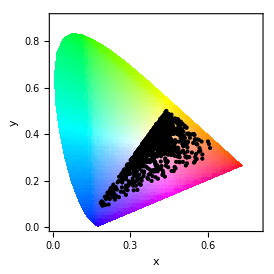

```mathematica
ChromaticityPlot[XYZColor@@@RandomPoint[ConvexHullMesh[Flatten[innerColors,1]],1000],PlotStyle->Black]
```

The inside colors cover much less of the greens. Let’s combine these ingredients.

#### Mixture

Some appropriately colored apple slices:

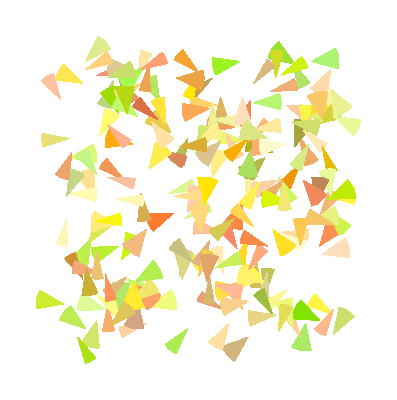

```mathematica
appleImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/8,Pi/4}]}]},200]]
```

Some carrot shavings:

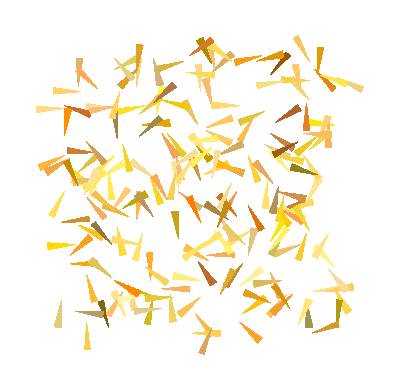

```mathematica
carrotImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,1,{#[[1]],#[[1]]+#[[2]]}&@{RandomReal[{0,2Pi}],RandomReal[{Pi/16,Pi/12}]}]},200]]
```

A few blueberries:

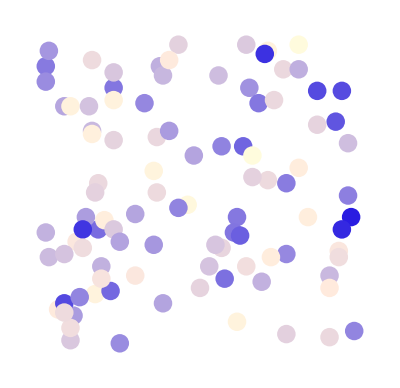

```mathematica
berryImage=Graphics[Table[{XYZColor@RandomPoint[fruitColorHull[]],Disk[RandomInteger[{0,100},2]/10,0.3]},100]]
```

And the combination:

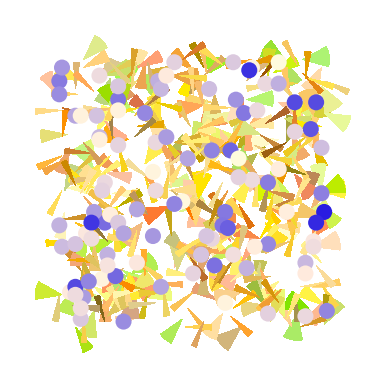

```mathematica
combo=Show[appleImage,carrotImage,berryImage]
```

Let’s put the ingredients in the blender to make our smoothie.

```mathematica
im=Rasterize[combo];
Manipulate[Blur[im,i],{i,2,50}]
```

Or we can cross the ingredients with a blender...

```mathematica
ImageRestyle[im,-Graphics-]
```

-Graphics-

This concludes our stroll through food data.